## 5. From Uniformly Continuous to Regular

```mathematica
FindInstance[0≤θ0≤π/2∧0≤ξ≤θ0∧Cos[θ0-ξ]≤2Cos[θ0]∧0≤θ≤θ0∧0≤ξprime≤ξ∧¬(Cos[θ-ξprime]≤2Cos[θ]),{θ0,ξ,ξprime,θ}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[0≤θ0≤π/2&&0≤ξ≤θ0&&Cos[θ0-ξ]≤2 Cos[θ0]&&0≤θ≤θ0&&0≤ξprime≤ξ&&Cos[θ-ξprime]>2 Cos[θ],{θ0,ξ,ξprime,θ}]

```mathematica
Function[{θ0},FindInstance[0≤ξ≤θ0∧Cos[θ0-ξ]≤2Cos[θ0]∧0≤θ≤θ0∧0≤ξprime≤ξ∧¬(Cos[θ-ξprime]≤2Cos[θ]),{ξ,ξprime,θ}]]/@{0,π/6,π/5,π/4,π/3,(2π)/5,π/2}
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

{{},{},{},{},{},FindInstance[0≤ξ≤(2 π)/5&&Sin[π/10+ξ]≤1/2 (-1+√5)&&0≤θ≤(2 π)/5&&0≤ξprime≤ξ&&Cos[θ-ξprime]>2 Cos[θ],{ξ,ξprime,θ}],FindInstance[0≤ξ≤π/2&&Sin[ξ]≤0&&0≤θ≤π/2&&0≤ξprime≤ξ&&Cos[θ-ξprime]>2 Cos[θ],{ξ,ξprime,θ}]}

```mathematica
Function[{θ0},Resolve[∀_({ξ,ξprime,θ},0≤ξ≤θ0∧Cos[θ0-ξ]≤2Cos[θ0]∧0≤θ≤θ0∧0≤ξprime≤ξ)Cos[θ-ξprime]≤2Cos[θ]]][0]
```

True

```mathematica
Function[{θ0},Resolve[∀_({ξ,ξprime,θ},0≤ξ≤θ0∧Cos[θ0-ξ]≤2Cos[θ0]∧0≤θ≤θ0∧0≤ξprime≤ξ)Cos[θ-ξprime]≤2Cos[θ]]][π/6]
```

$Aborted

```mathematica
sphericalPlot3D[r_,θ_,ϕ_]:=SphericalPlot3D[r,π/2-θ,ϕ]
```

```mathematica
Manipulate[ParametricPlot3D[FromSphericalCoordinates[{{1,π/2-ArcTan[Tan[θ0]Cos[φ]],φ},{1,π/2,φ}}],{φ,0,2π}],{θ0,0,π/2}]
```

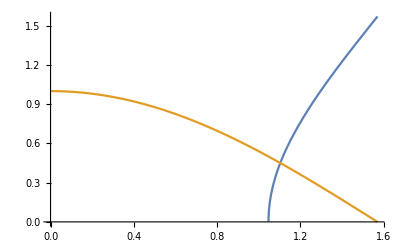

```mathematica
Plot[{ArcCos[2Cos[θ]],Cos[θ]},{θ,π/2,0}]
```

```mathematica
TableForm[{#,N[#]}&/@NestList[ArcCos[Cos[#]/2]&,π/3,10]]
```

π/3 | 1.0472
ArcCos[1/4] | 1.31812
ArcCos[1/8] | 1.44547
ArcCos[1/16] | 1.50826
ArcCos[1/32] | 1.53954
ArcCos[1/64] | 1.55517
ArcCos[1/128] | 1.56298
ArcCos[1/256] | 1.56689
ArcCos[1/512] | 1.56884
ArcCos[1/1024] | 1.56982
ArcCos[1/2048] | 1.57031

```mathematica
text[t_,ψ_]:=Text[t,ψ,FormatType->TraditionalForm]
Graphics3D[{Opacity[0.5],Sphere[{0,0,0}],InfinitePlane[Prepend[#,{0,0,0}]]&/@{{{1,1,0},{0,0,1}},{{1,-1,0},{0,0,1}},{{0,1,1},{1,0,0}},{{0,1,-1},{1,0,0}},{{1,0,1},{0,1,0}},{{-1,0,1},{0,1,0}}},{Arrow[{{0,0,0},#}],,text[#,1.4#]}&/@{{0,0,1},{1/(√3),1/(√3),1/(√3)},{1/(√3),-1/(√3),1/(√3)},{1/(√2),1/(√2),0},{1/(√2),-1/(√2),0}}}]
```

-Graphics3D-